```mathematica
p[1]={{0,0},{11,0},{11,3},{7,3},{7,1},{4,1},{4,2},{0,2},{0,0}};
```

```mathematica
p[2]={{0,0},{4,0},{4,1},{7,1},{7,-1},{11,-1},{11,2},{0,2},{0,0}};
```

```mathematica
p[3]={{0,0},{3,0},{3,11},{1,11},{1,7},{2,7},{2,4},{0,4},{0,0}};
```

```mathematica
p[4]={{0,0},{2,0},{2,4},{1,4},{1,7},{3,7},{3,11},{0,11},{0,0}};
```

```mathematica
p[5]={{0,0},{4,0},{4,2},{7,2},{7,1},{11,1},{11,3},{0,3},{0,0}};
```

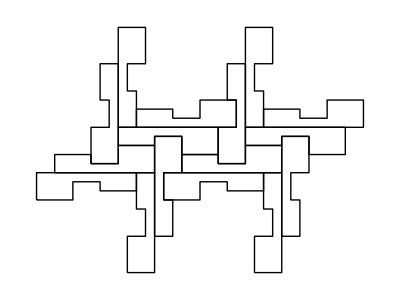

```mathematica
Graphics[{Line[p[1]],Line[Map[{7,3}+#&,p[2]]],Line[Map[{14,0}+#&,p[1]]],Line[Map[{21,3}+#&,p[2]]],Line[Map[{4,1}+#&,p[3]]],Line[Map[{18,1}+#&,p[3]]],Line[Map[{11,-7}+#&,p[4]]],Line[Map[{25,-7}+#&,p[4]]],Line[Map[{12,-3}+#&,p[5]]],Line[Map[{-2,-3}+#&,p[5]]],Line[Map[{8,-11}+#&,p[3]]],Line[Map[{22,-11}+#&,p[3]]],Line[Map[{9,5}+#&,p[1]]],Line[Map[{23,5}+#&,p[1]]],Line[Map[{7,5}+#&,p[4]]],Line[Map[{21,5}+#&,p[4]]]}]
```